```mathematica
Clear[μ,B]
μ=5;
a=50*B;
o=20*B;
Y1[y_]:=2(1-y^2)(x^4(2*x^2+a*y))/((2*x^2+a*y)^2+(2*o*x)^2)
A1[B_ ]:=NIntegrate[Y1[y]*1/4 1/Cosh[(x-μ)/2]^2,{x,-20,20},{y,-1,1}]
Y2[y_]:=(2 a x^2 y (2 a^2-4 x^4+a x^2 y)+(a^2-4 x^4)^2 Log[Abs[2 x^2+a y]])/a^3
A2[B_ ]:=NIntegrate[(Y2[1]-Y2[-1])1/4 1/Cosh[(x-μ)/2]^2,{x,-20,20}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

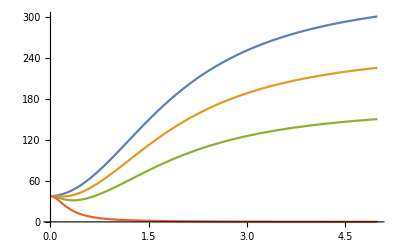

```mathematica
σ[θ_,B_]:=(A1[B] Sin[θ]^2+A2[B] Cos[θ]^2)
Plot[{σ[0,B],σ[π/6,B],σ[π/4,B],σ[π/2,B]},{B,0.001,5}]
```

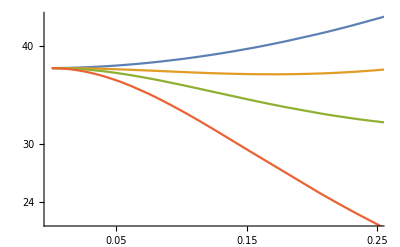

-Graphics-

-Graphics-

```mathematica
Show[%1,BaseStyle->{FontFamily->"Times",FontSize->18},PlotRange->{{0,.25},{22,43}},Ticks->{{0.05,0.15,0.25},{24,30,40}},AxesOrigin->{0,21.3}]
```

```mathematica
Show[%10,BaseStyle->{FontFamily->"Times",FontSize->40},PlotRange->{{0,.25},{37.1,37.69}},Ticks->{{0.1,.25},{37.3,37.7}},AxesOrigin->{0,37.08}]
```

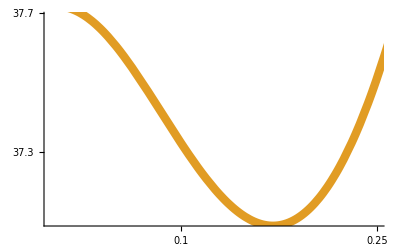

```mathematica
Clear[μ,B]
μ=5;
a1=90*B;
o1=20*B;
Y1[y_,a_,o_]:=2(1-y^2)(x^4(2*x^2+a*y))/((2*x^2+a*y)^2+(2*o*x)^2)
A1[a_,o_]:=NIntegrate[Y1[y,a,o]*1/4 1/Cosh[(x-μ)/2]^2,{x,-20,20},{y,-1,1}]
Y2[y_,a_]:=(2 a x^2 y (2 a^2-4 x^4+a x^2 y)+(a^2-4 x^4)^2 Log[Abs[2 x^2+a y]])/a^3
A2[a_]:=NIntegrate[(Y2[1,a]-Y2[-1,a])1/4 1/Cosh[(x-μ)/2]^2,{x,-20,20}]
```

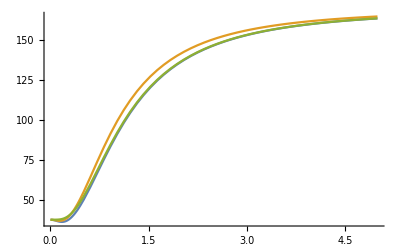

```mathematica
σ[θ_,a_,o_]:=(A1[a,o] Sin[θ]^2+A2[a] Cos[θ]^2)
Plot[{σ[π/4,90*B,20*B],σ[π/4,100*B,20*B],σ[π/4,90*B,15*B]},{B,0.001,5}]
```

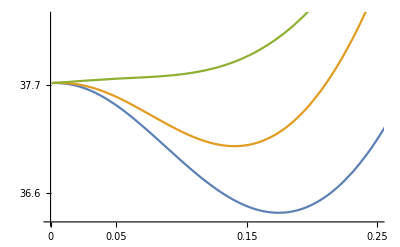

-Graphics-

```mathematica
Show[%16,BaseStyle->{FontFamily->"Times",FontSize->18},PlotRange->{{0,0.25},{36.3,38.4}},Ticks->{{0,0.05,0.15,0.25},{36.6,37.7}},AxesOrigin->{0,36.3}]
```

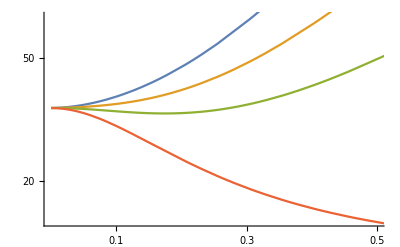

-Graphics-

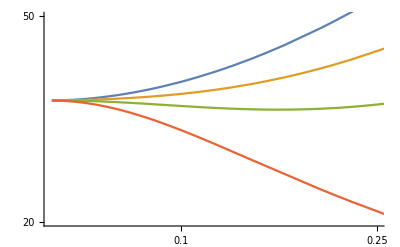

```mathematica
Show[%18,BaseStyle->{FontFamily->"Times",FontSize->30},PlotRange->{{0,.25},{20,50}},Ticks->{{0.1,0.3,0.25},{20,50,80}},AxesOrigin->{0,8}]
```

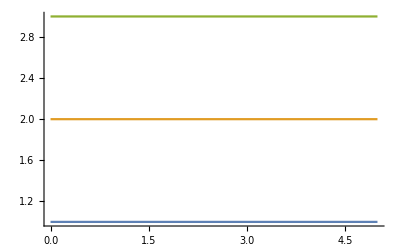

```mathematica
Plot[{1,2,3},{x,0,5}]
```